```mathematica
h=1/2
V=10
```

1/2

10

```mathematica
Divisors[V]
```

{1,2,5,10}

```mathematica
eqs={x'[t]==V*Cos[b[t]]-(V/h)*y[t],
y'[t]==V*Sin[b[t]],
b'[t]==(V/h)*Cos[b[t]]^2}
```

{x'[t]==10 Cos[b[t]]-20 y[t],y'[t]==10 Sin[b[t]],b'[t]==20 Cos[b[t]]^2}

```mathematica
sol=ParametricNDSolve[Join[eqs,{x[0]==-8,y[0]==0,b[0]==b0}],{x,y,b},{t,0,20},{b0}]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>],b→ParametricFunction[<>]}

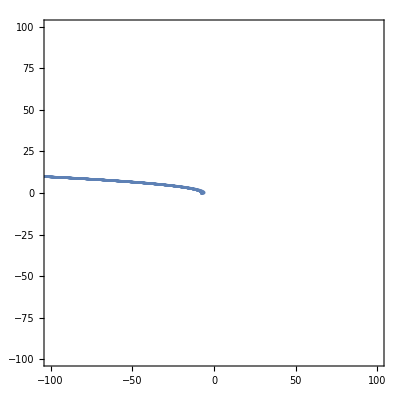

```mathematica
ParametricPlot[Table[{x[b0][t],y[b0][t]}/.sol,{b0,-1,1,0.1}],{t,0,20},Frame->True,PlotRange->{{-100,100},{-100,100}}]
```